```mathematica
(* questo e' un commento *)
```

```mathematica
(* il piu' classico degli esempi *)
Print["hello"]
```

hello

```mathematica
(* in matematica abbiamo un solo tipo : le espressioni *)
FullForm[x^2+3]
```

Plus[3,Power[x,2]]

```mathematica
(* le assegnazioni equivalgono ad incrementare l'insieme di regole
di trasformazione che l'interprete decide di applicare a un'espressione quando la valuta *)

x=2
```

2

```mathematica
FullForm[x^2+3]
```

7

```mathematica
y=2
x=2^y
```

2

4

```mathematica
x^4
```

16

```mathematica
y=10
```

10

```mathematica
x:=2^y
```

```mathematica
x^4
```

1099511627776

```mathematica
?y
```

```mathematica
?y
```

```mathematica
f[x_]:=x^2+x+1+y
```

```mathematica
f[3]
```

24

```mathematica
y=11
```

11

```mathematica
X=Range[1000];
```

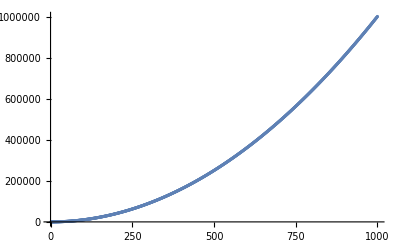

```mathematica
ListPlot[Map[f,X]]
```

```mathematica
X=Import["http://www.repubblica.it"];
X2=Import["http://www.corriere.it"];
```

```mathematica
AlphaTest[x_]:=0≤x≤25
```

```mathematica
XN=Select[
ToCharacterCode[
ToUpperCase[X]]-65,AlphaTest];
```

```mathematica
XN2=Select[
ToCharacterCode[
ToUpperCase[X2]]-65,AlphaTest];
```

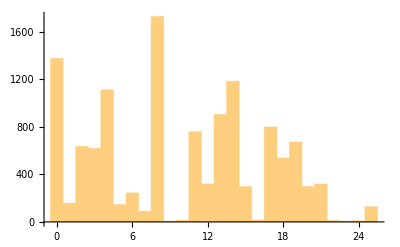

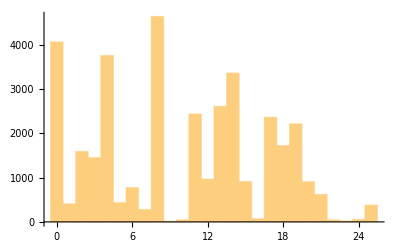

```mathematica
Histogram[XN,26]
Histogram[XN2,26]
```